```mathematica
ab[n_]:=Mod[3^Abs[n],4]
```

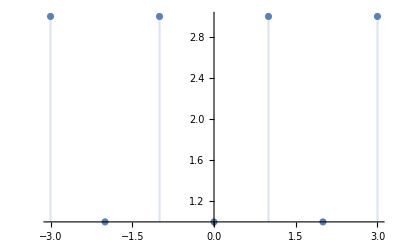

```mathematica
DiscretePlot[{a[x]},{x,-3,3}]
```

```mathematica
a[0]
```

1

```mathematica
a[1]
```

3

```mathematica
a[2]
```

1

```mathematica
a[3]
```

3

```mathematica
a[-1]
```

3

```mathematica
a[-2]
```

1

```mathematica
FunctionPeriod[a[x]]
```

0

```mathematica
f[t_]:=(Cos[t+π/4])^6+(Sin[3t+π/2])^6
```

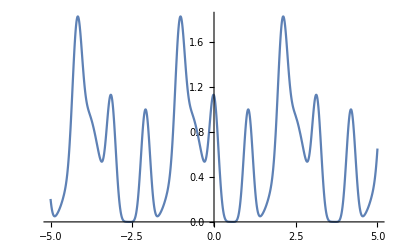

```mathematica
Plot[{f[x]},{x,-5,5}]
```

```mathematica
FunctionPeriod[f[x],x]
```

π

```mathematica
L=π/2
```

π/2

```mathematica
a0= 1/(2*L)∫_-L^L (f[x])ⅆx
```

5/8

```mathematica
a[n_]:=1/(π/2)∫_(-π/2)^(π/2) (f[x]*Cos[(n*x*π)/(π/2)])ⅆx
```

```mathematica
a[2]
```

```mathematica
a[0]
```

5/4

```mathematica
b[n_]:=1/L*∫_-L^L f[x]*Sin[(n*x*π)/L]ⅆx
```

```mathematica
d3=a0+∑_(n=1)^20 (a[n]*Cos[(n*x*π)/L]+b[n]*Sin[(n*x*π)/L])
```

$Aborted

```mathematica
cn[n_]:= 1/L∫_-L^L f[x]*ⅇ^(-ⅈ*(n*π*x)/L)ⅆx
```

```mathematica
sum=∑_(n=-20)^20 cn[n]*ⅇ^(ⅈ*(n*π*x)/L)
```

5/4-15/32 ⅈ ⅇ^(-2 ⅈ x)+15/32 ⅈ ⅇ^(2 ⅈ x)-3/16 ⅇ^(-4 ⅈ x)-3/16 ⅇ^(4 ⅈ x)+(15/32+ⅈ/32) ⅇ^(-6 ⅈ x)+(15/32-ⅈ/32) ⅇ^(6 ⅈ x)+3/16 ⅇ^(-12 ⅈ x)+3/16 ⅇ^(12 ⅈ x)+1/32 ⅇ^(-18 ⅈ x)+1/32 ⅇ^(18 ⅈ x)

```mathematica
sum
```

5/4-15/32 ⅈ ⅇ^(-2 ⅈ x)+15/32 ⅈ ⅇ^(2 ⅈ x)-3/16 ⅇ^(-4 ⅈ x)-3/16 ⅇ^(4 ⅈ x)+(15/32+ⅈ/32) ⅇ^(-6 ⅈ x)+(15/32-ⅈ/32) ⅇ^(6 ⅈ x)+3/16 ⅇ^(-12 ⅈ x)+3/16 ⅇ^(12 ⅈ x)+1/32 ⅇ^(-18 ⅈ x)+1/32 ⅇ^(18 ⅈ x)

```mathematica
L=π/2
```

π/2

```mathematica
g[t_]:=(Cos[t])^6+(Sin[t])^4
```

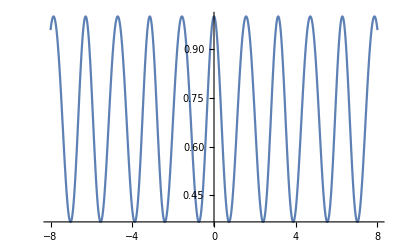

```mathematica
Plot[{g[x]},{x,-8,8}]
```

```mathematica
g'[t]
```

-6 Cos[t]^5 Sin[t]+4 Cos[t] Sin[t]^3

```mathematica
g1[x_]:=(-6 Cos[t])^5 *Sin[t]+4 Cos[t]*( Sin[t])^3
```

SetDelayed::write: Tag Plus in (-6 Cos[t]^5 Sin[t]+4 Cos[t] Sin[t]^3)[x_] is Protected.

$Failed

```mathematica
g2=g''[t]
```

-6 Cos[t]^6+12 Cos[t]^2 Sin[t]^2+30 Cos[t]^4 Sin[t]^2-4 Sin[t]^4

```mathematica
cn2[n_]:=  1/(2*L)∫_-L^L (-6 Cos[x]^5 Sin[x]+4 Cos[x] Sin[x]^3)*ⅇ^(-ⅈ*(n*π*x)/L)ⅆx
```

```mathematica
sum=∑_(n=-20)^20 cn2[n]*ⅇ^(ⅈ*(n*π*x)/L)
```

1/32 ⅈ ⅇ^(-2 ⅈ x)-1/32 ⅈ ⅇ^(2 ⅈ x)-5/8 ⅈ ⅇ^(-4 ⅈ x)+5/8 ⅈ ⅇ^(4 ⅈ x)-3/32 ⅈ ⅇ^(-6 ⅈ x)+3/32 ⅈ ⅇ^(6 ⅈ x)